Testing the idea to see if the GRIN tube polarization is aligned.

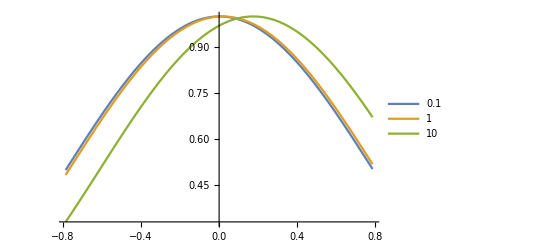

```mathematica
angles=π/180{0.1,1,10};
Plot[Evaluate[Table[Cos[θ-θp ]^2,{θp,angles}]],{θ,-π/4,π/4},PlotLegends->180/π angles]
```

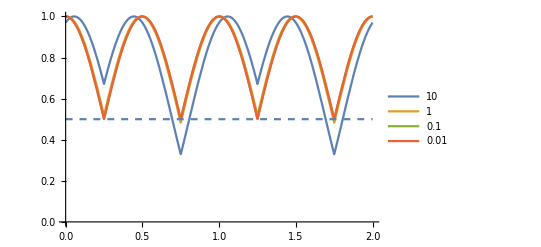

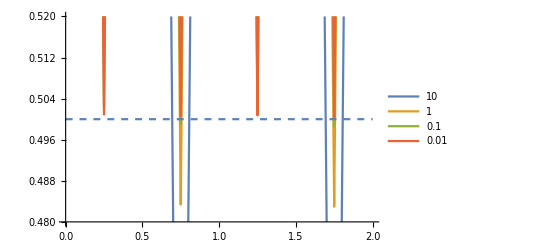

```mathematica
angles=π/180{10,1,0.1,0.01};
θ=π/4 TriangleWave[t];
Show[Plot[Evaluate[Table[Cos[θ-θp ]^2,{θp,angles}]],{t,0,2},PlotLegends->180/π angles,PlotRange->{0,1}],Plot[0.5,{t,0,2},PlotStyle->Dashed]]
Show[Plot[Evaluate[Table[Cos[θ-θp ]^2,{θp,angles}]],{t,0,2},PlotLegends->180/π angles,PlotRange->{0.48,.52}],Plot[0.5,{t,0,2},PlotStyle->Dashed]]
```

The Thorlabs K10CR1 rotation controller adds the following uncertainty:

```mathematica
"Unidirectional repeatability, +/- degs"
0.00006*180/π
"Backlash, +/- degs"
0.0002*180/π
"Repeatable incremental movement, degs"
0.03
"Absolute accuracy, degs"
0.14
```

Unidirectional repeatability, +/- degs

0.00343775

Backlash, +/- degs

0.0114592

Repeatable incremental movement, degs

0.03

Absolute accuracy, degs

0.14

I don’t think the absolute accuracy is relevant because we are not trying to move the stage to a particular degree mark, but move 45 deg relative to something. Not sure if the repeatable incremental movement is relevant either. I would guess based on this our uncertainty is at least 0.01 deg just from the Thorlabs K10CR1.

Computing the angular error given the difference in transmission through the polarizer at +/- 45 degrees (see my Field Notes 2022.12.03):

```mathematica
ang=(4-√(16-4(3/2-d)))/2
```

1/2 (4-√(16-4 (3/2-d)))

```mathematica
err = 0.01*π/180
diff=Cos[err+π/4]^2-Cos[err-π/4]^2
"estimated error"
-0.5diff
```

0.000174533

-0.000349066

estimated error

0.000174533

```mathematica
(1-t-t^2)-(1+t-t^2)
```

-2 t

```mathematica
Series[Cos[t+π/4]^2-Cos[t-π/4]^2,{t,0,2}]
```

-2 t+O[t]^3